```mathematica
ClearAll[EI,α,γ,m,a,b,d,g,μ,Q,W,s,c,R,nφ,ΚMat,S,𝒞𝒻,𝒞,β,p,P,Κ,EIlimit,Δr,r0,CoeffiMat,rN,r,BMat,AMat,DMat,Bbar,Abar,rMat,mMat,Dbar,MMat,FMat,MeMat,Λ,MνMat,LMat,GMat0];EI[Ν_]:= Sum[Sum[α[i,n]* Κ[i,n](r[n-1]^(m[i,n]+2)-r[n]^(m[i,n]+2)),{i,4}]+γ[n](r[n-1]^4-r[n]^4),{n,Ν}]
α[i_,n_]:=π/(𝒞[n][[3,3]])1/(m[i,n]+2)(𝒞[n][[1,3]]+𝒞[n][[2,3]](m[i,n]+1)-𝒞[n][[3,4]]*g[i,n]*m[i,n])
γ[n_]:=π/(𝒞[n][[3,3]])1/4(μ[1,n](𝒞[n][[1,3]]+3𝒞[n][[2,3]])-2μ[2,n]*𝒞[n][[3,4]]-1)
m[1,n_]:=Sqrt[(-b[n]+Sqrt[b[n]^2-4a[n]*d[n]])/(2 a[n])]
m[2,n_]:=Sqrt[(-b[n]-Sqrt[b[n]^2-4a[n]*d[n]])/(2 a[n])]
m[3,n_]:=-Sqrt[(-b[n]+Sqrt[b[n]^2-4a[n]*d[n]])/(2 a[n])]
m[4,n_]:=-Sqrt[(-b[n]-Sqrt[b[n]^2-4a[n]*d[n]])/(2 a[n])]
a[n_]:=β[n][[2,2]]*β[n][[4,4]]-(β[n][[2,4]])^2
b[n_]:=β[n][[2,4]](2β[n][[1,4]]+β[n][[2,4]]+2β[n][[5,6]])+(β[n][[1,4]])^2-β[n][[4,4]](β[n][[1,1]]+2β[n][[1,2]]+β[n][[2,2]]+β[n][[6,6]])-β[n][[2,2]]*β[n][[5,5]]
d[n_]:=β[n][[5,5]](β[n][[1,1]]+2β[n][[1,2]]+β[n][[2,2]]+β[n][[6,6]])-(β[n][[5,6]])^2
g[i_,n_]:=1/m[i,n](β[n][[2,4]]*m[i,n]^3+(β[n][[1,4]]+β[n][[2,4]])m[i,n]^2-β[n][[5,6]]*m[i,n])/(β[n][[4,4]] m[i,n]^2-β[n][[5,5]])
μ[1,n_]:=1/(𝒞[n][[3,3]])(((𝒞[n][[1,3]]-𝒞[n][[2,3]])*(-4*β[n][[4,4]]+β[n][[5,5]]))/((-2*β[n][[1,4]]-6*β[n][[2,4]]+β[n][[5,6]])*(2*β[n][[1,4]]-2*β[n][[2,4]]+β[n][[5,6]])-(4*β[n][[4,4]]-β[n][[5,5]])*(-β[n][[1,1]]-2*β[n][[1,2]]+3*β[n][[2,2]]-β[n][[6,6]]))+(2*𝒞[n][[3,4]]*(2*β[n][[1,4]]-2*β[n][[2,4]]+β[n][[5,6]]))/((-2*β[n][[1,4]]-6*β[n][[2,4]]+β[n][[5,6]])*(2*β[n][[1,4]]-2*β[n][[2,4]]+β[n][[5,6]])-(4*β[n][[4,4]]-β[n][[5,5]])*(-β[n][[1,1]]-2*β[n][[1,2]]+3*β[n][[2,2]]-β[n][[6,6]])));
μ[2,n_]:=
1/(𝒞[n][[3,3]])(((𝒞[n][[1,3]]-𝒞[n][[2,3]])*(-2*β[n][[1,4]]-6*β[n][[2,4]]+β[n][[5,6]]))/((-2*β[n][[1,4]]-6*β[n][[2,4]]+β[n][[5,6]])*(2*β[n][[1,4]]-2*β[n][[2,4]]+β[n][[5,6]])-(4*β[n][[4,4]]-β[n][[5,5]])*(-β[n][[1,1]]-2*β[n][[1,2]]+3*β[n][[2,2]]-β[n][[6,6]]))+(2*𝒞[n][[3,4]]*(β[n][[1,1]]+2*β[n][[1,2]]-3*β[n][[2,2]]+β[n][[6,6]]))/((-2*β[n][[1,4]]-6*β[n][[2,4]]+β[n][[5,6]])*(2*β[n][[1,4]]-2*β[n][[2,4]]+β[n][[5,6]])-(4*β[n][[4,4]]-β[n][[5,5]])*(-β[n][[1,1]]-2*β[n][[1,2]]+3*β[n][[2,2]]-β[n][[6,6]])));
Q[i_,n_]:=1/m[i,n](β[n][[1,2]]*m[i,n]+ β[n][[2,2]]*m[i,n](m[i,n]+1)-β[n][[2,4]]*g[i,n] m[i,n]^2  )
Q[5,n_]:=μ[1,n](β[n][[1,2]]+3 β[n][[2,2]])-2 μ[2,n] *β[n][[2,4]]+ (𝒞[n][[2,3]])/(𝒞[n][[3,3]])
W[i_,n_]:=1/m[i,n](β[n][[5,5]]*g[i,n]- β[n][[5,6]])
W[5,n_]:=1/2(β[n][[5,5]]*μ[2,n]-β[n][[5,6]]*μ[1,n])
Bbar[n_]:={
{1,1,1,1}
,{g[1,n-1] ,g[2,n-1] ,g[3,n-1] ,g[4,n-1] }
,{Q[1,n-1],Q[2,n-1],Q[3,n-1],Q[4,n-1]}
,{W[1,n-1] ,W[2,n-1]  ,W[3,n-1] ,W[4,n-1] }}
Abar[n_]:={
{1,1,1,1}
,{g[1,n] ,g[2,n] ,g[3,n] ,g[4,n] }
,{Q[1,n],Q[2,n],Q[3,n],Q[4,n]}
,{W[1,n] ,W[2,n]  ,W[3,n] ,W[4,n] }}
(*rMat[q_,n_]:={{r[q]^m[1,n],0,0,0},{0,r[q]^m[2,n],0,0},{0,0,r[q]^m[3,n],0},{0,0,0,r[q]^m[4,n]}}*)
mMat[n_]:={{m[1,n],0,0,0},{0,m[2,n],0,0},{0,0,m[3,n],0},{0,0,0,m[4,n]}}
Dbar[n_]:={μ[1,n]-μ[1,n-1],μ[2,n]-μ[2,n-1],Q[5,n]-Q[5,n-1],W[5,n]-W[5,n-1]}
MMat[n_]:=Inverse[Abar[n]].Bbar[n].mMat[n-1].Inverse[Bbar[n]].Abar[n]
FMat[n_]:=Inverse[Abar[n]].(-2 IdentityMatrix[4]+Bbar[n].mMat[n-1].Inverse[Bbar[n]]).Dbar[n]
(*MeMat[n_]:=MMat[n]*)
MeMat[n_]:=MMat[n]+mMat[n]
Λ[n_]:=Eigenvalues[Transpose[MeMat[n]]]/2
MνMat[n_]:=Eigenvectors[Transpose[MeMat[n]]]
LMat[n_]:=MνMat[n].FMat[n]/2
(*GMat0[n_]:=Inverse[MνMat[n]].LMat[n]/(2-Λ[n])*)
GMat0[n_]:=Inverse[MνMat[n]].(LMat[n]/(2-Λ[n]))
s[φ_]:= Sin[φ];
c[φ_]:= Cos[φ];
R[φ_]:= {{1,0,0,0,0,0}
,{0,c[φ]^2,s[φ]^2,2s[φ]*c[φ],0,0}
,{0,s[φ]^2,c[φ]^2,-2 s[φ]*c[φ],0,0}
,{0,-s[φ]*c[φ],s[φ] *c[φ] ,c[φ]^2-s[φ]^2,0,0}
,{0,0,0,0,c[φ],-s[φ]}
,{0,0,0,0,s[φ],c[φ]}};
p[n_]:= g[1,n](g[3,n]-g[4,n])(m[1,n]-m[3,n])(m[2,n]-m[4,n])+g[2,n](g[3,n]-g[4,n])(m[2,n]-m[3,n])(m[4,n]-m[1,n])-(g[1,n] g[2,n]+g[3,n] g[4,n]-g[1,n] g[4,n] - g[2,n] g[4,n])(m[1,n]-m[2,n])(m[3,n]-m[4,n]);P[1,n_]:=-1/p[n]((g[2,n] g[3,n] (m[2,n]-m[3,n])(m[4,n]-2)+g[2,n] g[4,n] (m[4,n]-m[2,n])(m[3,n]-2)
+g[3,n] g[4,n] (m[3,n]-m[4,n])(m[2,n]-2))μ[1,n] +(g[2,n](m[3,n]-m[4,n])(m[2,n]-2)
+g[3,n](m[4,n]-m[2,n])(m[3,n]-2)+g[4,n](m[2,n]-m[3,n])(m[4,n]-2))μ[2,n]);
P[2,n_]:=
1/p[n]((g[1,n] g[3,n] (m[1,n]-m[3,n])(m[4,n]-2)+g[1,n] g[4,n] (m[4,n]-m[1,n])(m[3,n]-2)
+g[3,n] g[4,n] (m[3,n]-m[4,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[3,n]-m[4,n])(m[1,n]-2)
+g[3,n](m[4,n]-m[1,n])(m[3,n]-2)+g[4,n](m[1,n]-m[3,n])(m[4,n]-2))μ[2,n]);
P[3,n_]:=
-1/p[n]((g[1,n] g[2,n] (m[1,n]-m[2,n])(m[4,n]-2)+g[1,n] g[4,n] (m[4,n]-m[1,n])(m[2,n]-2)
+g[2,n] g[4,n] (m[2,n]-m[4,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[2,n]-m[4,n])(m[1,n]-2)
+g[2,n](m[4,n]-m[1,n])(m[2,n]-2)+g[4,n](m[1,n]-m[2,n])(m[4,n]-2))μ[2,n]);
P[4,n_]:=
1/p[n]((g[1,n] g[2,n] (m[1,n]-m[2,n])(m[3,n]-2)+g[1,n] g[3,n] (m[3,n]-m[1,n])(m[2,n]-2)
+g[2,n] g[3,n] (m[2,n]-m[3,n])(m[1,n]-2))μ[1,n] +(g[1,n](m[2,n]-m[3,n])(m[1,n]-2)
+g[2,n](m[3,n]-m[1,n])(m[2,n]-2)+g[3,n](m[1,n]-m[2,n])(m[3,n]-2))μ[2,n]);
CoeffiMat[n_]:= {
{r[n]^(m[1,n]-2),r[n]^(m[2,n]-2),r[n]^(m[3,n]-2),r[n]^(m[4,n]-2)}
,{g[1,n] r[n]^(m[1,n]-2),g[2,n] r[n]^(m[2,n]-2),g[3,n] r[n]^(m[3,n]-2),g[4,n] r[n]^(m[4,n]-2)}
,{r[n-1]^(m[1,n]-2),r[n-1]^(m[2,n]-2),r[n-1]^(m[3,n]-2),r[n-1]^(m[4,n]-2)}
,{g[1,n] r[n-1]^(m[1,n]-2),g[2,n]  r[n-1]^(m[2,n]-2),g[3,n] r[n-1]^(m[3,n]-2),g[4,n] r[n-1]^(m[4,n]-2)}}
(*Κ[i_,n_]:=P[i,n] r[n]^(-m[i,n]+2)*)
μMat[n_]:={-μ[1,n],-μ[2,n],-μ[1,n],-μ[2,n]};
ΚMat[n_] := LinearSolve[CoeffiMat[n],μMat[n]];
```

#### Homogeneous material and no friction interface

```mathematica
Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=1;
φ0=25./180 π;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
nφ[n_]:=φ0;
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EIlimit=-(rN^4-r0^4)/4(Sum[α[i,1]*P[i,1](m[i,1]+2),{i,4}]+4γ[1]);
{EI[Νl],EIlimit}
]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.314148,31.8087,8.28618×10^7,818356.},{0.0715769,-1404.18,7.86039×10^6,-4.30962×10^6},{0.18531,153.989,3.37272×10^11,4.05873×10^8},{0.042222,-6797.8,3.19942×10^10,-2.13741×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{234.723,230.189}

```mathematica
EIofN[nl_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
φ0=25./180 π;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[nl];
nφ[n_]:=φ0;
S= 10^-4{{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EI[nl]
]
```

```mathematica
EIofN/@Range[30]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.314148,31.8087,8.28618×10^7,818356.},{0.0715769,-1404.18,7.86039×10^6,-4.30962×10^6},{0.18531,153.989,3.37272×10^11,4.05873×10^8},{0.042222,-6797.8,3.19942×10^10,-2.13741×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{234.723,231.6,230.845,230.565,230.431,230.358,230.313,230.284,230.264,230.25,230.24,230.231,230.225,230.22,230.216,230.213,230.21,230.208,230.206,230.204,230.203,230.202,230.2,230.2,230.199,230.198,230.197,230.197,230.196,230.196}

## Cubic Orthotropic

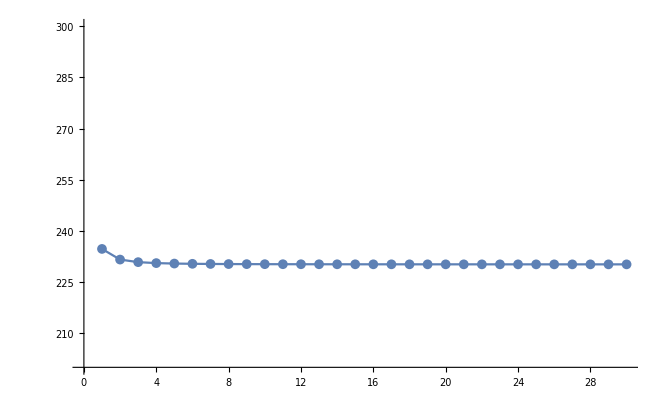

```mathematica
ListLinePlot[%41,PlotRange->{200,300},PlotMarkers->{Automatic, 10}]
```

#### Heterogeneous material and no friction interface

```mathematica
Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=2;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
(*φ0=-15./180 π;*)
(*nφ[n_]:=φ0;*)
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
{φ1,φ2} = {-15./180 π,25./180 π};
nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;
Κ[i_,n_]:=ΚMat[n][[i]];
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EIlimit1=-(rN^4-r0^4)/4(Sum[α[i,1]*P[i,1](m[i,1]+2),{i,4}]+4γ[1]);
EIlimit2=-(rN^4-r0^4)/4(Sum[α[i,2]*P[i,2](m[i,2]+2),{i,4}]+4γ[2]);
EIlimit=(EIlimit1+EIlimit2)/2.;
{EI[Νl],EIlimit}
]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.192928,85.3842,1.26545×10^9,2.85932×10^6},{-0.0326559,7994.38,-9.18321×10^7,1.89982×10^7},{0.120287,306.133,5.1959×10^11,2.0416×10^8},{-0.0203604,28662.7,-3.7706×10^10,1.3565×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{234.664,244.996}

```mathematica
EIofN2[nl_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ];
r0=2*10^-3;
rN=14*10^-3;
Νl=2;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[nl];
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
{φ1,φ2} = {-15./180 π,25./180 π};
nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
EI[nl]
]
```

```mathematica
EIofN2/@Range[10]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.640507,8.27737,4.06409×10^7,3.14482×10^6},{0.346861,-33.3357,7.1624×10^6,-4.24444×10^6},{0.52279,21.6929,1.19551×10^11,2.88112×10^9},{0.283112,-87.3646,2.10692×10^10,-3.88854×10^9}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{881.471,498.429,678.698,517.729,629.784,530.495,610.207,538.24,599.844,543.337}

#### Heterogeneous material and no slip interface

```mathematica
Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ,BMat,AMat,DMat,GMat];
r0=2*10^-3;
rN=14*10^-3;
Νl=10;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[Νl];
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
(*S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};*)
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {-15./180 π,25./180 π};*)
{φ1,φ2} = {25./180 π,-25./180 π};
nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
BMat[n_]:=BMat[n]={
{r[n-1]^m[1,n-1],r[n-1]^m[2,n-1],r[n-1]^m[3,n-1],r[n-1]^m[4,n-1]}
,{g[1,n-1] r[n-1]^m[1,n-1],g[2,n-1] r[n-1]^m[2,n-1],g[3,n-1] r[n-1]^m[3,n-1],g[4,n-1] r[n-1]^m[4,n-1]}
,{Q[1,n-1] r[n-1]^m[1,n-1],Q[2,n-1] r[n-1]^m[2,n-1],Q[3,n-1] r[n-1]^m[3,n-1],Q[4,n-1] r[n-1]^m[4,n-1]}
,{W[1,n-1] r[n-1]^m[1,n-1],W[2,n-1]  r[n-1]^m[2,n-1],W[3,n-1] r[n-1]^m[3,n-1],W[4,n-1] r[n-1]^m[4,n-1]}};
AMat[n_]:=AMat[n]={
{r[n-1]^m[1,n],r[n-1]^m[2,n],r[n-1]^m[3,n],r[n-1]^m[4,n]}
,{g[1,n] r[n-1]^m[1,n],g[2,n] r[n-1]^m[2,n],g[3,n] r[n-1]^m[3,n],g[4,n] r[n-1]^m[4,n]}
,{Q[1,n] r[n-1]^m[1,n],Q[2,n] r[n-1]^m[2,n],Q[3,n] r[n-1]^m[3,n],Q[4,n] r[n-1]^m[4,n]}
,{W[1,n] r[n-1]^m[1,n],W[2,n]  r[n-1]^m[2,n],W[3,n] r[n-1]^m[3,n],W[4,n] r[n-1]^m[4,n]}};
DMat[n_]:=DMat[n]=-r[n-1]^2{μ[1,n]-μ[1,n-1],μ[2,n]-μ[2,n-1],Q[5,n]-Q[5,n-1],W[5,n]-W[5,n-1]};
ABMat = ConstantArray[0.0,{4*Νl,4*Νl}];
DDMat = ConstantArray[0.0,4*Νl];
ABMat[[1;;2,1;;4]]=r0^2 CoeffiMat[1][[3;;4,1;;4]];
ABMat[[-2;;-1,-4;;-1]]=rN^2 CoeffiMat[Νl][[1;;2,1;;4]];
DDMat[[1;;2]]=r0^2{μ[1,1],μ[2,1]};
DDMat[[-2;;-1]]=rN^2{μ[1,Νl],μ[2,Νl]};
Do[
row = 2+(n-2)*4;
colB = (n-2)*4;
colA = (n-1)*4;
ABMat[[(row+1);;(row+4),(colB+1);;(colB+4)]]=BMat[n];
ABMat[[(row+1);;(row+4),(colA+1);;(colA+4)]]=-AMat[n];
DDMat[[(row+1);;(row+4)]] = DMat[n]
,{n,2,Νl}];
KKMat =LinearSolve[ABMat,-DDMat];
Κ[i_,n_]:=KKMat[[i+(n-1)*4]];
Block[{},
ClearAll[YMat,eq1,eq2,eq3,eq4,Solsc];
YMat[n_,rad_]:= LMat[n]/(2-Λ[n])rad^2+{c1 rad^(Λ[n][[1]]),c2 rad^(Λ[n][[2]]),c3 rad^(Λ[n][[3]]),c4 rad^(Λ[n][[4]])};
(*YMat[n_,rad_]:= LMat[n]/(4-Λ[n])rad^2+{c1 rad^((Λ[n][[1]])/2),c2 rad^((Λ[n][[2]])/2),c3 rad^((Λ[n][[3]])/2),c4 rad^((Λ[n][[4]])/2)};*)
eq1 =Simplify[Total[Inverse[MνMat[1]].YMat[1,r0]]]==-r0^2 μ[1,1];
eq2 = Simplify[(Inverse[MνMat[1]].YMat[1,r0]).{g[1,1],g[2,1],g[3,1],g[4,1]}]==-r0^2 μ[2,1];
eq3 =Simplify[ Total[Inverse[MνMat[1]].YMat[1,rN]]]==-rN^2 μ[1,1];
eq4 = Simplify[(Inverse[MνMat[1]].YMat[1,rN]).{g[1,1],g[2,1],g[3,1],g[4,1]}]==-rN^2 μ[2,1];
Solsc[1]=NSolve[eq1&&eq2&&eq3&&eq4,{c1,c2,c3,c4}];
GMat[1]=Inverse[MνMat[1]].DiagonalMatrix[{c1,c2,c3,c4}/.Solsc[1][[1]]];
eq1 =Simplify[ Total[Inverse[MνMat[2]].YMat[2,r0]]]==-r0^2 μ[1,2];
eq2 = Simplify[(Inverse[MνMat[2]].YMat[2,r0]).{g[1,2],g[2,2],g[3,2],g[4,2]}]==-r0^2 μ[2,2];
eq3 =Simplify[ Total[Inverse[MνMat[2]].YMat[2,rN]]]==-rN^2 μ[1,2];
eq4 = Simplify[(Inverse[MνMat[2]].YMat[2,rN]).{g[1,2],g[2,2],g[3,2],g[4,2]}]==-rN^2 μ[2,2];
Solsc[2]=NSolve[eq1&&eq2&&eq3&&eq4,{c1,c2,c3,c4}];
GMat[2]=Inverse[MνMat[2]].DiagonalMatrix[{c1,c2,c3,c4}/.Solsc[2][[1]]];
];
EIlimit = -1/8(Sum[α[i,1](m[i,1]+2)GMat0[1][[i]]+α[i,2](m[i,2]+2)GMat0[2][[i]],{i,4}]+4(γ[1]+γ[2]))(rN^4-r0^4)-(*1/2 Sum[Sum[(2α[i,1](m[i,1]+2)GMat[1][[i,j]])/(4+Λ[1][[j]])(rN^(2+(Λ[1][[j]])/2)-r0^(2+(Λ[1][[j]])/2))+(2α[i,2](m[i,2]+2)GMat[2][[i,j]])/(4+Λ[2][[j]])(rN^(2+(Λ[2][[j]])/2)-r0^(2+(Λ[2][[j]])/2)),{j,4}],{i,4}];*)
1/2 Sum[Sum[(α[i,1](m[i,1]+2)GMat[1][[i,j]])/(2+Λ[1][[j]])(rN^(2+Λ[1][[j]])-r0^(2+Λ[1][[j]]))+(α[i,2](m[i,2]+2)GMat[2][[i,j]])/(2+Λ[2][[j]])(rN^(2+Λ[2][[j]])-r0^(2+Λ[2][[j]])),{j,4}],{i,4}];
{EI[Νl],EIlimit}
]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{8.6853×10^-8,0.0000556774,1.15137×10^7,17960.6,0.,0.,0.,0.,0.,0.,«30»},{-1.00584×10^-7,0.000108033,-6.13378×10^6,14368.1,0.,0.,0.,0.,0.,0.,«30»},«7»,{0.,0.,0.,0.,1.62751×10^-16,-9.6428×10^-14,-0.000189241,8.8288×10^-7,1.62751×10^-16,-9.6428×10^-14,«30»},«30»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{1.1581,-1.94035,0.532737,-0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{2.38162×10^-10,-4.99772×10^-10,-1.29321×10^-10,1.70346×10^-10}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,1.,1.,1.},{-1.1581,1.94035,-0.532737,0.799978},{2.66174×10^-10,3.82842×10^-10,-1.34332×10^-10,-1.21628×10^-10},{-2.38162×10^-10,4.99772×10^-10,1.29321×10^-10,-1.70346×10^-10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{833.367,841.084}

```mathematica
EIofN3[nl_]:=Block[{(*r0,rN,Νl,φ0,Δr*)},
ClearAll[𝒞,β,Δr,r,nφ,BMat,AMat,DMat];
r0=2*10^-3;
rN=14*10^-3;
Δr[n_]:= (rN-r0)/n;
r[n_]:=r0 +n*Δr[nl];
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
{φ1,φ2} = {25./180 π,-25./180 π};
nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;
𝒞[n_]:=𝒞[n]=𝒞𝒻[nφ[n]];
β[n_]:=β[n]=
Table[𝒞[n][[i,j]]-((𝒞[n][[i,3]])*(𝒞[n][[3,j]]))/(𝒞[n][[3,3]]),{i,6},{j,6}];
BMat[n_]:=BMat[n]={
{r[n-1]^m[1,n-1],r[n-1]^m[2,n-1],r[n-1]^m[3,n-1],r[n-1]^m[4,n-1]}
,{g[1,n-1] r[n-1]^m[1,n-1],g[2,n-1] r[n-1]^m[2,n-1],g[3,n-1] r[n-1]^m[3,n-1],g[4,n-1] r[n-1]^m[4,n-1]}
,{Q[1,n-1] r[n-1]^m[1,n-1],Q[2,n-1] r[n-1]^m[2,n-1],Q[3,n-1] r[n-1]^m[3,n-1],Q[4,n-1] r[n-1]^m[4,n-1]}
,{W[1,n-1] r[n-1]^m[1,n-1],W[2,n-1]  r[n-1]^m[2,n-1],W[3,n-1] r[n-1]^m[3,n-1],W[4,n-1] r[n-1]^m[4,n-1]}};
AMat[n_]:=AMat[n]={
{r[n-1]^m[1,n],r[n-1]^m[2,n],r[n-1]^m[3,n],r[n-1]^m[4,n]}
,{g[1,n] r[n-1]^m[1,n],g[2,n] r[n-1]^m[2,n],g[3,n] r[n-1]^m[3,n],g[4,n] r[n-1]^m[4,n]}
,{Q[1,n] r[n-1]^m[1,n],Q[2,n] r[n-1]^m[2,n],Q[3,n] r[n-1]^m[3,n],Q[4,n] r[n-1]^m[4,n]}
,{W[1,n] r[n-1]^m[1,n],W[2,n]  r[n-1]^m[2,n],W[3,n] r[n-1]^m[3,n],W[4,n] r[n-1]^m[4,n]}};
DMat[n_]:=DMat[n]=-r[n-1]^2{μ[1,n]-μ[1,n-1],μ[2,n]-μ[2,n-1],Q[5,n]-Q[5,n-1],W[5,n]-W[5,n-1]};
ABMat = ConstantArray[0.0,{4*nl,4*nl}];
DDMat = ConstantArray[0.0,4*nl];
ABMat[[1;;2,1;;4]]=r0^2 CoeffiMat[1][[3;;4,1;;4]];
ABMat[[-2;;-1,-4;;-1]]=r[nl]^2 CoeffiMat[nl][[1;;2,1;;4]];
DDMat[[1;;2]]=r0^2{μ[1,1],μ[2,1]};
DDMat[[-2;;-1]]=r[nl]^2{μ[1,nl],μ[2,nl]};
Do[
row = 2+(n-2)*4;
colB = (n-2)*4;
colA = (n-1)*4;
ABMat[[(row+1);;(row+4),(colB+1);;(colB+4)]]=BMat[n];
ABMat[[(row+1);;(row+4),(colA+1);;(colA+4)]]=-AMat[n];
DDMat[[(row+1);;(row+4)]] = DMat[n]
,{n,2,nl}];
KKMat =LinearSolve[ABMat,-DDMat];
Κ[i_,n_]:=KKMat[[i+(n-1)*4]];
EI[nl]
]
```

```mathematica
res1=EIofN3/@Range[30]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{8.6853×10^-8,0.0000556774,1.15137×10^7,17960.6},{-1.00584×10^-7,0.000108033,-6.13378×10^6,14368.1},{0.0000141183,0.00119615,70829.9,836.014},{-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{8.6853×10^-8,0.0000556774,1.15137×10^7,17960.6,0.,0.,0.,0.},{-1.00584×10^-7,0.000108033,-6.13378×10^6,14368.1,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,0.0000163504,-0.00232095,37733.7,-668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{8.6853×10^-8,0.0000556774,1.15137×10^7,17960.6,0.,0.,0.,0.,0.,0.,«2»},{-1.00584×10^-7,0.000108033,-6.13378×10^6,14368.1,0.,0.,0.,0.,0.,0.,«2»},«7»,{0.,0.,0.,0.,1.39427×10^-15,-3.51739×10^-13,-0.0000220899,2.42039×10^-7,1.39427×10^-15,-3.51739×10^-13,«2»},«2»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{528.111,671.281,760.063,794.155,810.517,819.85,825.286,829.063,831.475,833.367,834.633,835.716,836.458,837.136,837.605,838.059,838.374,838.693,838.913,839.146,839.306,839.482,839.601,839.738,839.829,839.937,840.008,840.095,840.151,840.222}

```mathematica
(res1-1046.9395611647633)/1046.9395611647633
```

{-0.158049,-0.324017,0.0371065,-0.134556,0.0441092,-0.0815406,0.0382081,-0.0578364,0.0325784,-0.0446145,0.0281287,-0.0362392,0.024657,-0.0304787,0.0219096,-0.0262822,0.0196944,-0.0230927,0.0178761,-0.0205884,0.0163595,-0.0185711,0.0150767,-0.0169118,0.0139783,-0.0155234,0.0130276,-0.0143448,0.0121971,-0.0133319}

```mathematica
EIofN3/@Range[10]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.},«6»,{0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,«2»},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,«2»},«8»,«2»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,«6»},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,«6»},«8»,«6»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{881.471,707.714,1085.79,906.068,1093.12,961.572,1086.94,986.388,1081.05,1000.23}

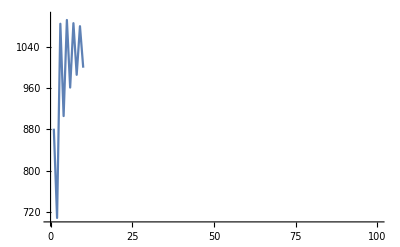

```mathematica
ListLinePlot[{881.4714440961833,707.7137814220032,1085.787875403896,906.0676982408797,1093.1191941723418,961.5715068934211,1086.9411302557494,986.3883715859139,1081.0472204612056,1000.2308935334687},PlotRange->{{0,100},{700,1100}}]
```

## CMat from Weilin’s code

```mathematica
NotebookDirectory[]
```

/Users/wenqiangfang/Dropbox (Brown)/Research/CurvilinerOrthogrophy/

```mathematica
CMatString = {{"C11","C12","C13","C14",0.0,0.0},{"C12","C22","C23","C24",0.0,0.0},{"C13","C23","C33","C34",0.0,0.0},{"C14","C24","C34","C44",0.0,0.0},{0.0,0.0,0.0,0.0,"C55","C56"},{0.0,0.0,0.0,0.0,"C56","C66"}};
```

```mathematica
ExchangeRule25=Import["/Users/wenqiangfang/Dropbox (Brown)/Research/CurvilinerOrthogrophy/CurvilinearAnisotropyBeams/Code/Weilin_code&notes/Codes/MFiles_Feb22_No_friction/CMat_CurvOrtho65.dat"];
ExchangeRule15=Import["/Users/wenqiangfang/Dropbox (Brown)/Research/CurvilinerOrthogrophy/CurvilinearAnisotropyBeams/Code/Weilin_code&notes/Codes/MFiles_Feb22_No_friction/CMat_CurvOrtho105.dat"];
ExchangeRule0=Import["/Users/wenqiangfang/Dropbox (Brown)/Research/CurvilinerOrthogrophy/CurvilinearAnisotropyBeams/Code/Weilin_code&notes/Codes/MFiles_Feb22_No_friction/CMat_CurvOrtho90.dat"];
```

```mathematica
rules25 = (#[[1]]->#[[2]])&/@ExchangeRule25;
rules15 = (#[[1]]->#[[2]])&/@ExchangeRule15;
rules0 = (#[[1]]->#[[2]])&/@ExchangeRule0;
CMat25 = CMatString/.rules25;
CMat15 = CMatString/.rules15;
CMat0 = CMatString/.rules0;
```

```mathematica
𝒞25= Table[Evaluate[10^-6 CMat25[[m,n]]]&,{m,6},{n,6}];
𝒞15= Table[Evaluate[10^-6 CMat15[[m,n]]]&,{m,6},{n,6}];
𝒞0= Table[Evaluate[10^-6 Chop[CMat0[[m,n]]]]&,{m,6},{n,6}];
𝒞25//MatrixForm
𝒞15//MatrixForm
𝒞0//MatrixForm
```

(1.05×10^-10& | -6.69×10^-12& | -8.05×10^-12& | -1.61×10^-12& | 0.& | 0.&
-6.69×10^-12& | 1.36×10^-10& | -4.51×10^-11& | 2.26×10^-11& | 0.& | 0.&
-8.05×10^-12& | -4.51×10^-11& | 7.32×10^-11& | -9.74×10^-11& | 0.& | 0.&
-1.61×10^-12& | 2.26×10^-11& | -9.74×10^-11& | 2.57×10^-10& | 0.& | 0.&
0.& | 0.& | 0.& | 0.& | 4.55×10^-10& | 9.58×10^-11&
0.& | 0.& | 0.& | 0.& | 9.58×10^-11& | 2.95×10^-10&)

(1.05×10^-10& | -6.46×10^-12& | -8.28×10^-12& | 1.05×10^-12& | 0.& | 0.&
-6.46×10^-12& | 1.26×10^-10& | -2.46×10^-11& | -2.83×10^-11& | 0.& | 0.&
-8.28×10^-12& | -2.46×10^-11& | 4.18×10^-11& | 7.71×10^-11& | 0.& | 0.&
1.05×10^-12& | -2.83×10^-11& | 7.71×10^-11& | 3.39×10^-10& | 0.& | 0.&
0.& | 0.& | 0.& | 0.& | 4.83×10^-10& | -6.25×10^-11&
0.& | 0.& | 0.& | 0.& | -6.25×10^-11& | 2.67×10^-10&)

(1.05263×10^-10& | -6.31579×10^-12& | -8.42105×10^-13& | 0& | 0& | 0&
-6.31579×10^-12& | 1.17647×10^-10& | -9.41177×10^-12& | 0& | 0& | 0&
-8.42105×10^-13& | -9.41177×10^-12& | 2.×10^-11& | 0& | 0& | 0&
0& | 0& | 0& | 4.×10^-10& | 0& | 0&
0& | 0& | 0& | 0& | 5.×10^-10& | 0&
0& | 0& | 0& | 0& | 0& | 2.23158×10^-10&)

### CMat from rotation

```mathematica
(*φ0=0/180 π;*)
(*φ0=25/180 π;*)
φ0=-15/180 π;
nφ[n_]:=φ0;
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
𝒞𝒻[φ_]:=10^-6 Transpose[Inverse[R[φ]]].S.Inverse[R[φ]];
(*{φ1,φ2} = {π,π}*)
(*nφ[n_]:=Mod[n,2](φ1-φ2)+φ2;*)
𝒞=Table[Evaluate[𝒞𝒻[nφ[#]][[m,n]]]&,{m,6},{n,6}];
Table[ScientificForm[𝒞[[m,n]],3],{m,6},{n,6}]//MatrixForm
```

(1.05×10^-10& | -6.46×10^-12& | -8.28×10^-12& | 1.05×10^-12& | 0.& | 0.&
-6.46×10^-12& | 1.27×10^-10& | -2.46×10^-11& | -2.82×10^-11& | 0.& | 0.&
-8.28×10^-12& | -2.46×10^-11& | 4.18×10^-11& | 7.72×10^-11& | 0.& | 0.&
1.05×10^-12& | -2.82×10^-11& | 7.72×10^-11& | 3.39×10^-10& | 0.& | 0.&
0.& | 0.& | 0.& | 0.& | 4.83×10^-10& | -6.25×10^-11&
0.& | 0.& | 0.& | 0.& | -6.25×10^-11& | 2.67×10^-10&)

## Derivation

```mathematica
binv =Inverse[{{b^(m1-2),b^(m2-2),b^(m3-2),b^(m4-2)}
,{g1 b^(m1-2),g2 b^(m2-2),g3 b^(m3-2),g4 b^(m4-2)}
,{(b-Δb)^(m1-2),(b-Δb)^(m2-2),(b-Δb)^(m3-2),(b-Δb)^(m4-2)}
,{g1(b-Δb)^(m1-2),g2 (b-Δb)^(m2-2),g3(b-Δb)^(m3-2),g4(b-Δb)^(m4-2)}}]//Simplify;
```

```mathematica
μmat =  {-μ1,-μ2,-μ1,-μ2};
```

```mathematica
Kres = Limit[binv.μmat//Simplify,Δb->0,Direction->"FromAbove"]//Simplify;
```

```mathematica
Kres//MatrixForm
```

((b^(2-m1) (g3 g4 (-2+m2) (m3-m4) μ1-g3 (-2+m3) (m2-m4) μ2+g4 (m2-m3) (-2+m4) μ2+g2 (-g4 (-2+m3) (m2-m4) μ1+g3 (m2-m3) (-2+m4) μ1+(-2+m2) (m3-m4) μ2)))/(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4))
-(b^(2-m2) (g3 g4 (-2+m1) (m3-m4) μ1-g3 (-2+m3) (m1-m4) μ2+g4 (m1-m3) (-2+m4) μ2+g1 (-g4 (-2+m3) (m1-m4) μ1+g3 (m1-m3) (-2+m4) μ1+(-2+m1) (m3-m4) μ2)))/(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4))
(b^(2-m3) (g2 g4 (-2+m1) (m2-m4) μ1-g2 (-2+m2) (m1-m4) μ2+g4 (m1-m2) (-2+m4) μ2+g1 (-g4 (-2+m2) (m1-m4) μ1+g2 (m1-m2) (-2+m4) μ1+(-2+m1) (m2-m4) μ2)))/(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4))
(b^(2-m4) (-g2 g3 (-2+m1) (m2-m3) μ1+g2 (-2+m2) (m1-m3) μ2-g3 (m1-m2) (-2+m3) μ2+g1 (g3 (-2+m2) (m1-m3) μ1-g2 (m1-m2) (-2+m3) μ1-(-2+m1) (m2-m3) μ2)))/(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4)))

```mathematica
Kres[[1]]*pp/b^(2-m1)//FullSimplify
```

g3 g4 (-2+m2) (m3-m4) μ1+g2 (g3 (m2-m3) (-2+m4)+g4 (-2+m3) (-m2+m4)) μ1-g3 (-2+m3) (m2-m4) μ2+g2 (-2+m2) (m3-m4) μ2+g4 (m2-m3) (-2+m4) μ2

```mathematica
Kres[[2]]*pp/b^(2-m2)//FullSimplify
```

g1 (g4 (-2+m3) (m1-m4)-g3 (m1-m3) (-2+m4)) μ1-g3 g4 (-2+m1) (m3-m4) μ1+g3 (-2+m3) (m1-m4) μ2-g1 (-2+m1) (m3-m4) μ2-g4 (m1-m3) (-2+m4) μ2

```mathematica
Kres[[3]]*pp/b^(2-m3)//FullSimplify
```

g2 g4 (-2+m1) (m2-m4) μ1+g1 (g2 (m1-m2) (-2+m4)+g4 (-2+m2) (-m1+m4)) μ1-g2 (-2+m2) (m1-m4) μ2+g1 (-2+m1) (m2-m4) μ2+g4 (m1-m2) (-2+m4) μ2

```mathematica
Kres[[4]]*pp/b^(2-m4)//FullSimplify
```

g1 (g3 (-2+m2) (m1-m3)-g2 (m1-m2) (-2+m3)) μ1-g2 g3 (-2+m1) (m2-m3) μ1+g2 (-2+m2) (m1-m3) μ2-g1 (-2+m1) (m2-m3) μ2-g3 (m1-m2) (-2+m3) μ2

```mathematica
pp=(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4))
```

g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4)

```mathematica
Kres*(g1 (g4 (m2-m3) (m1-m4)-g3 (m1-m3) (m2-m4)+g2 (m1-m2) (m3-m4))+g2 g3 (m2-m3) (m1-m4)-g2 g4 (m1-m3) (m2-m4)+g3 g4 (m1-m2) (m3-m4))
```

{b^(2-m1) (g3 g4 (-2+m2) (m3-m4) μ1-g3 (-2+m3) (m2-m4) μ2+g4 (m2-m3) (-2+m4) μ2+g2 (-g4 (-2+m3) (m2-m4) μ1+g3 (m2-m3) (-2+m4) μ1+(-2+m2) (m3-m4) μ2)),-b^(2-m2) (g3 g4 (-2+m1) (m3-m4) μ1-g3 (-2+m3) (m1-m4) μ2+g4 (m1-m3) (-2+m4) μ2+g1 (-g4 (-2+m3) (m1-m4) μ1+g3 (m1-m3) (-2+m4) μ1+(-2+m1) (m3-m4) μ2)),b^(2-m3) (g2 g4 (-2+m1) (m2-m4) μ1-g2 (-2+m2) (m1-m4) μ2+g4 (m1-m2) (-2+m4) μ2+g1 (-g4 (-2+m2) (m1-m4) μ1+g2 (m1-m2) (-2+m4) μ1+(-2+m1) (m2-m4) μ2)),b^(2-m4) (-g2 g3 (-2+m1) (m2-m3) μ1+g2 (-2+m2) (m1-m3) μ2-g3 (m1-m2) (-2+m3) μ2+g1 (g3 (-2+m2) (m1-m3) μ1-g2 (m1-m2) (-2+m3) μ1-(-2+m1) (m2-m3) μ2))}

```mathematica
Inverse[
{{-2β[[1,4]]-6β[[2,4]]+β[[5,6]],4β[[4,4]]-β[[5,5]]}
,{-β[[1,1]]-2β[[1,2]]+3β[[2,2]]-β[[6,6]],2β[[1,4]]-2β[[2,4]]+β[[5,6]]}
}
]
```

Part::partd: Part specification β⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦5,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
{{(2 β⟦1,4⟧-2 β⟦2,4⟧+β⟦5,6⟧)/((-2 β⟦1,4⟧-6 β⟦2,4⟧+β⟦5,6⟧) (2 β⟦1,4⟧-2 β⟦2,4⟧+β⟦5,6⟧)-(4 β⟦4,4⟧-β⟦5,5⟧) (-β⟦1,1⟧-2 β⟦1,2⟧+3 β⟦2,2⟧-β⟦6,6⟧)),(-4 β⟦4,4⟧+β⟦5,5⟧)/((-2 β⟦1,4⟧-6 β⟦2,4⟧+β⟦5,6⟧) (2 β⟦1,4⟧-2 β⟦2,4⟧+β⟦5,6⟧)-(4 β⟦4,4⟧-β⟦5,5⟧) (-β⟦1,1⟧-2 β⟦1,2⟧+3 β⟦2,2⟧-β⟦6,6⟧))},{(β⟦1,1⟧+2 β⟦1,2⟧-3 β⟦2,2⟧+β⟦6,6⟧)/((-2 β⟦1,4⟧-6 β⟦2,4⟧+β⟦5,6⟧) (2 β⟦1,4⟧-2 β⟦2,4⟧+β⟦5,6⟧)-(4 β⟦4,4⟧-β⟦5,5⟧) (-β⟦1,1⟧-2 β⟦1,2⟧+3 β⟦2,2⟧-β⟦6,6⟧)),(-2 β⟦1,4⟧-6 β⟦2,4⟧+β⟦5,6⟧)/((-2 β⟦1,4⟧-6 β⟦2,4⟧+β⟦5,6⟧) (2 β⟦1,4⟧-2 β⟦2,4⟧+β⟦5,6⟧)-(4 β⟦4,4⟧-β⟦5,5⟧) (-β⟦1,1⟧-2 β⟦1,2⟧+3 β⟦2,2⟧-β⟦6,6⟧))}}//InputForm
```

Part::partd: Part specification β⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦5,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
  (-4*β[[4,4]] + β[[5,5]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}, 
 {(β[[1,1]] + 2*β[[1,2]] - 3*β[[2,2]] + β[[6,6]])/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
  (-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}}

```mathematica
ClearAll[𝒞]
```

```mathematica
{{(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
  (-4*β[[4,4]] + β[[5,5]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}, 
 {(β[[1,1]] + 2*β[[1,2]] - 3*β[[2,2]] + β[[6,6]])/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
  (-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])/((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*
     (2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - (4*β[[4,4]] - β[[5,5]])*
     (-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}}.{2𝒞[[3,4]],𝒞[[1,3]]-𝒞[[2,3]]}//InputForm
```

Part::partd: Part specification β⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification β⟦5,6⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{((𝒞[[1,3]] - 𝒞[[2,3]])*(-4*β[[4,4]] + β[[5,5]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])) + 
  (2*𝒞[[3,4]]*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
 ((𝒞[[1,3]] - 𝒞[[2,3]])*(-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])) + 
  (2*𝒞[[3,4]]*(β[[1,1]] + 2*β[[1,2]] - 3*β[[2,2]] + β[[6,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}

```mathematica
{((𝒞[[1,3]] - 𝒞[[2,3]])*(-4*β[[4,4]] + β[[5,5]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])) + 
  (2*𝒞[[3,4]]*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])), 
 ((𝒞[[1,3]] - 𝒞[[2,3]])*(-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]])) + 
  (2*𝒞[[3,4]]*(β[[1,1]] + 2*β[[1,2]] - 3*β[[2,2]] + β[[6,6]]))/
   ((-2*β[[1,4]] - 6*β[[2,4]] + β[[5,6]])*(2*β[[1,4]] - 2*β[[2,4]] + β[[5,6]]) - 
    (4*β[[4,4]] - β[[5,5]])*(-β[[1,1]] - 2*β[[1,2]] + 3*β[[2,2]] - β[[6,6]]))}
```

## Transverse isotropic S

```mathematica
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
```

```mathematica
Ep = 1/S[[1,1]]
Et = 1/S[[3,3]]
νp = -S[[1,2]] Ep
νtp = -S[[1,3]] Et
νpt = νtp Ep/Et
μt = 1/S[[4,4]]
μp = Ep/(2(1+νp))
```

9523.81

50000.

0.0601905

0.421

0.0801905

2500.

4491.56

```mathematica
S={{1/Ep,-νp/Ep,-νtp/Et,0,0,0}
,{-νp/Ep,1/Ep,-νtp/Et,0,0,0},
{-νpt/Ep,-νpt/Ep,1/Et,0,0,0},
{0,0,0,1/μt,0,0},
{0,0,0,0,1/μt,0},
{0,0,0,0,0,1/μp}}
```

{{0.000105,-6.32×10^-6,-8.42×10^-6,0,0,0},{-6.32×10^-6,0.000105,-8.42×10^-6,0,0,0},{-8.42×10^-6,-8.42×10^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264}}

```mathematica
S={{0.000105,-6.320000000000001*^-6,-8.42*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-8.42*^-6,0,0,0},{-8.42*^-6,-8.42*^-6,0.00002,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.00022264000000000002}};
S//MatrixForm
```

(0.000105 | -6.32×10^-6 | -8.42×10^-6 | 0 | 0 | 0
-6.32×10^-6 | 0.000105 | -8.42×10^-6 | 0 | 0 | 0
-8.42×10^-6 | -8.42×10^-6 | 0.00002 | 0 | 0 | 0
0 | 0 | 0 | 0.0004 | 0 | 0
0 | 0 | 0 | 0 | 0.0004 | 0
0 | 0 | 0 | 0 | 0 | 0.00022264)

## Isotropic S

```mathematica
S=10^-4 {{1.05,-0.0632,-0.0842,0.0,0.0,0.0}
,{-0.0632,1.18,-0.0941,0.0,0.0,0.0}
,{-0.0842,-0.0941,0.20,0.0,0.0,0.0}
,{0.0,0.0,0.0,4.0,0.0,0.0}
,{0.0,0.0,0.0,0.0,5.0,0.0}
,{0.0,0.0,0.0,0.0,0.0,2.5}};
```

```mathematica
Ep = 1/S[[1,1]]
Et = 1/S[[3,3]]
νp = -S[[1,2]] Ep
νtp = -S[[1,3]] Et
νpt = νtp Ep/Et
μt = 1/S[[4,4]]
μp = Ep/(2(1+νp))
```

9523.81

50000.

0.0601905

0.421

0.0801905

2500.

4491.56

```mathematica
Ep/(2(1+νp))
```

4491.56

```mathematica
S={{1/Ep,-νp/Ep,-νp/Ep,0,0,0}
,{-νp/Ep,1/Ep,-νp/Ep,0,0,0},
{-νp/Ep,-νp/Ep,1/Ep,0,0,0},
{0,0,0,1/μt,0,0},
{0,0,0,0,1/μt,0},
{0,0,0,0,0,1/μt}}
```

{{0.000105,-6.32×10^-6,-6.32×10^-6,0,0,0},{-6.32×10^-6,0.000105,-6.32×10^-6,0,0,0},{-6.32×10^-6,-6.32×10^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}}

```mathematica
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.0004,0,0},{0,0,0,0,0.0004,0},{0,0,0,0,0,0.0004}};
S//MatrixForm
```

(0.000105 | -6.32×10^-6 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | 0.000105 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | -6.32×10^-6 | 0.000105 | 0 | 0 | 0
0 | 0 | 0 | 0.0004 | 0 | 0
0 | 0 | 0 | 0 | 0.0004 | 0
0 | 0 | 0 | 0 | 0 | 0.0004)

```mathematica
S={{1/Ep,-νp/Ep,-νp/Ep,0,0,0}
,{-νp/Ep,1/Ep,-νp/Ep,0,0,0},
{-νp/Ep,-νp/Ep,1/Ep,0,0,0},
{0,0,0,1/μp,0,0},
{0,0,0,0,1/μp,0},
{0,0,0,0,0,1/μp}}
```

{{0.000105,-6.32×10^-6,-6.32×10^-6,0,0,0},{-6.32×10^-6,0.000105,-6.32×10^-6,0,0,0},{-6.32×10^-6,-6.32×10^-6,0.000105,0,0,0},{0,0,0,0.00022264,0,0},{0,0,0,0,0.00022264,0},{0,0,0,0,0,0.00022264}}

```mathematica
S={{0.000105,-6.320000000000001*^-6,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,0.000105,-6.320000000000001*^-6,0,0,0},{-6.320000000000001*^-6,-6.320000000000001*^-6,0.000105,0,0,0},{0,0,0,0.00022264000000000002,0,0},{0,0,0,0,0.00022264000000000002,0},{0,0,0,0,0,0.00022264000000000002}};
S//MatrixForm
```

(0.000105 | -6.32×10^-6 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | 0.000105 | -6.32×10^-6 | 0 | 0 | 0
-6.32×10^-6 | -6.32×10^-6 | 0.000105 | 0 | 0 | 0
0 | 0 | 0 | 0.00022264 | 0 | 0
0 | 0 | 0 | 0 | 0.00022264 | 0
0 | 0 | 0 | 0 | 0 | 0.00022264)

## Plot results

```mathematica
EIofN3/@Range[10]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.0000141183,0.00119615,70829.9,836.014},{0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.},«8»,{0.,0.,0.,0.,0.,0.,0.,0.,0.000125539,0.00162236,7965.63,616.384},{0.,0.,0.,0.,0.,0.,0.,0.,0.0000679847,-0.00653379,1403.83,-831.91}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{2.09116×10^-6,0.0000867718,478204.,11524.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.13245×10^-6,-0.000349459,84276.8,-15554.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«13»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0000163504,0.00232095,-37733.7,668.792}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{881.471,707.714,1085.79,906.068,1093.12,961.572,1086.94,986.388,1081.05,1000.23}